```mathematica
Quit[]
```

## Defining Functions And Interpolations

```mathematica
fSI[β_, q_, k_, c_, m_]:= -((4(1/4-β^2)q^2+3 m^2)/Sqrt[(1/4-β^2)q^2+m^2])ArcTan[(2Sqrt[m^2+(1/4-β^2)q^2])/(m^2-1+1/4 q^2-2β q k c + k^2)] + 2  (1+(-β q k c + β^2 q^2)/(k^2-2β q k c+β^2 q^2))+1/(2Sqrt[k^2-2β k q c+β^2 q^2])(1+2 m^2+(3/4-4 β^2)q^2-k^2+2β q k c+((1/4 q^2+m^2+1+k^2-2β q k c)(β q k c - β^2 q^2))/(k^2-2β q k c+q^2))*Log[(1+2Sqrt[k^2-2β k q c + β^2 q^2]+k^2-2 β k q c +1/4 q^2+m^2)/(1-2 Sqrt[k^2-2β k q c + β^2 q^2]+k^2-2 β k q c +1/4 q^2+m^2)]
```

```mathematica
fSIeff[k_]:= 1/(2Pi)NIntegrate[1/(2*.99)fSI[β, 105.658/238, k, c,138.039/238], {β, -1/2, 1/2}, {c, -.99, .99}, PrecisionGoal->4]
```

```mathematica
fSD[β_, q_, k_, c_, m_]:= 1/Sqrt[k^2-2β k q c+q^2](1/Sqrt[k^2-2β q k c+q^2]-(1+m^2+k^2-2 β k q c + 1/4 q^2)/(k^2-2β q k c+q^2))*Log[(1+2Sqrt[k^2-2β k q c + β^2 q^2]+k^2-2 β k q c +1/4 q^2+m^2)/(1-2 Sqrt[k^2-2β k q c + β^2 q^2]+k^2-2 β k q c +1/4 q^2+m^2)]
```

```mathematica
fSDeff[k_]:=-1/(2Pi)NIntegrate[1/(2*.99)fSD[β, 105.658/238, k, c,138.039/238], {β, -1/2, 1/2}, {c, -.99, .99}, PrecisionGoal->4]
```

```mathematica
AList = {.43418*10^-1,.60298*10^-1,.28950*10^-2,-.23522*10^-1,-.79791*10^-2,.23010*10^-2,.10794*10^-2,.12574*10^-3,-.13021*10^-3,.56563*10^-4,-.18011*10^-4,.42869*10^-5}
```

{0.043418,0.060298,0.002895,-0.023522,-0.0079791,0.002301,0.0010794,0.00012574,-0.00013021,0.000056563,-0.000018011,4.2869×10^-6}

```mathematica
fFourierBessel[r_]:=Piecewise[{{1/13 Sum[ AList[[n]]SphericalBesselJ[0,(n Pi r)/7.0],{n,12}],r≤7},{0,r>7}}]
```

```mathematica
fourierDensity[k_]:=(1/(197.327)^(3/2)NIntegrate[(4Pi)r^2 Sinc[(k r)/197.327]Sqrt[Abs[fFourierBessel[r]]], {r, 0, 7}])^2
```

```mathematica
fDensityInter=Interpolation[Table[{k,fourierDensity[238k]},{k,0,1,.005}]];
```

```mathematica
fSIeffInter = Interpolation[Table[{k,fSIeff[k]},{k,0,1,.005}]];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.74162 and 0.000302584 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.57604 and 0.000263797 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.42701 and 0.000312279 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

```mathematica
fSDeffInter = Interpolation[Table[{k,fSDeff[k]},{k,0,1,.005}]];
```

## Estimation of Errors and Fitting

```mathematica
RMSErrorInterSI=Interpolation[Table[{x,Sqrt[NIntegrate[1/(2Pi)^3(238)^3 4Pi k^2(fSIeffInter[k]-x)^2*fDensityInter[k],{k,0,1}]]/NIntegrate[1/(2Pi)^3(238)^3 4Pi k^2 fSIeffInter[k]*fDensityInter[k],{k,0,1}]},{x,.5,1.5,.01}]];
```

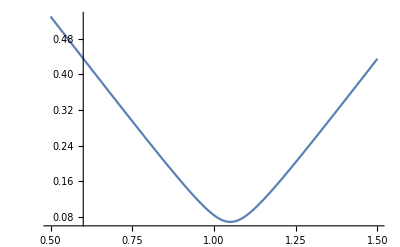

```mathematica
Plot[RMSErrorInterSI[x],{x,.5,1.5}]
```

```mathematica
FindMinimum[RMSErrorInterSI[x],{x,1.0}]
```

{0.068829,{x→1.05009}}

```mathematica
RMSErrorInterSD=Interpolation[Table[{x,Sqrt[NIntegrate[1/(2Pi)^3(238)^3 4Pi k^2(fSDeffInter[k]-x)^2*fDensityInter[k],{k,0,1}]]/NIntegrate[1/(2Pi)^3(238)^3 4Pi k^2 fSDeffInter[k]*fDensityInter[k],{k,0,1}]},{x,.5,1.5,.01}]];
```

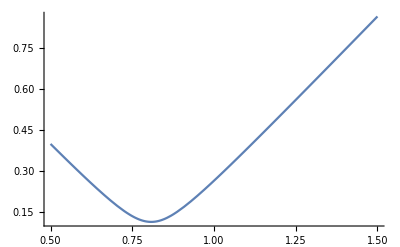

```mathematica
Plot[RMSErrorInterSD[x],{x,.5,1.5}]
```

```mathematica
FindMinimum[RMSErrorInterSD[x],{x,.8}]
```

{0.112358,{x→0.808022}}

## Plots

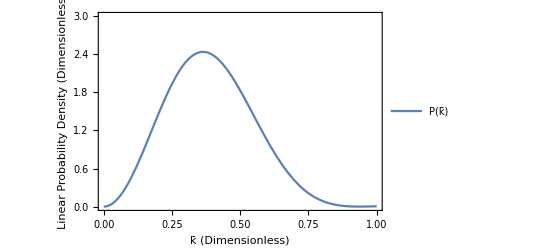

```mathematica
Plot[1/(2*Pi)^3 4Pi k^2(238)^3 fDensityInter[k],{k,0,1}, PlotRange->{0,3},Frame->True, FrameTicks->{{All, None}, {All, None}}, FrameTicksStyle->Directive[FontSize->12,FontColor->Black],FrameLabel->{{Style["Linear Probability Density \n (Dimensionless)",14,FontColor->Black], None},{Style["k̄ (Dimensionless)",14,FontColor->Black],None}} , RotateLabel->True, PlotLegends->Placed[{Style["P(k̄)",16,FontColor->Black]},{Right,Top}]]
```

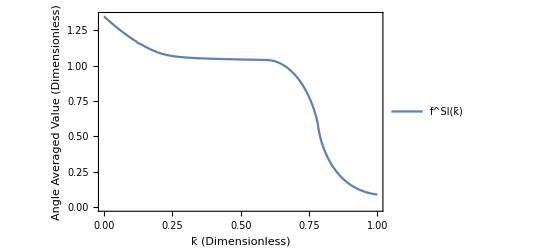

```mathematica
Plot[fSIeffInter[k],{k,0,1}, Frame->True, FrameTicks->{{All, None}, {All, None}}, FrameTicksStyle->Directive[FontSize->12,FontColor->Black],FrameLabel->{{Style["Angle Averaged Value \n (Dimensionless)",14,FontColor->Black], None},{Style["k̄ (Dimensionless)",14,FontColor->Black],None}} , RotateLabel->True, PlotLegends->Placed[{Style["f^SI(k̄)",16,FontColor->Black]},{Left,Bottom}]]
```

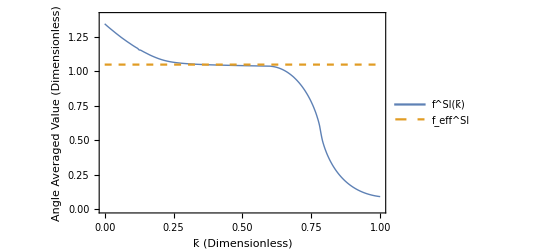

```mathematica
Plot[{fSIeffInter[k], 1.05009} ,{k, 0, 1}, PlotRange->{0,1.4},Frame->True, FrameTicks->{{All, None}, {All, None}}, FrameTicksStyle->Directive[FontSize->12,FontColor->Black],FrameLabel->{{Style["Angle Averaged Value \n (Dimensionless)",14,FontColor->Black], None},{Style["k̄ (Dimensionless)",14,FontColor->Black],None}} , RotateLabel->True, PlotLegends->Placed[{Style["f^SI(k̄)",16,FontColor->Black], Style[ToExpression["f^{SI}_{\\textrm{eff}}",TeXForm,HoldForm],16,FontColor->Black]},{Left,Bottom}], PlotStyle->{Thick, Dashed}]
```

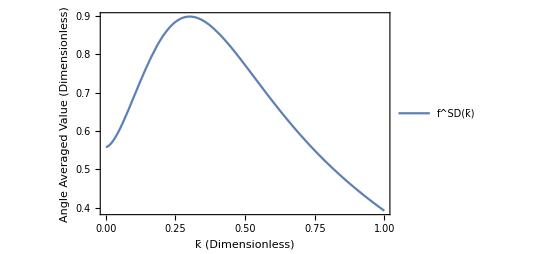

```mathematica
Plot[fSDeffInter[k], {k, 0, 1},Frame->True, FrameTicks->{{All, None}, {All,None}}, FrameTicksStyle->Directive[FontSize->12,FontColor->Black],FrameLabel->{{Style["Angle Averaged Value \n (Dimensionless)",14,FontColor->Black], None},{Style["k̄ (Dimensionless)",14,FontColor->Black],None}} , RotateLabel->True, PlotLegends->Placed[{Style["f^SD(k̄)",16,FontColor->Black]},{Left,Bottom}]]
```

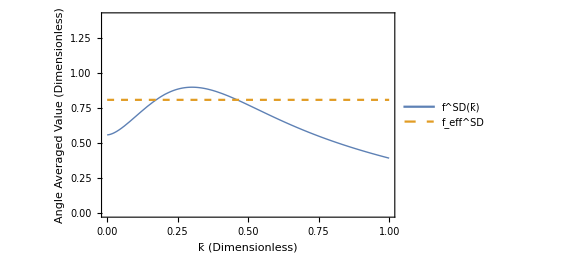

```mathematica
Plot[{fSDeffInter[k],.808022}, {k, 0, 1}, PlotRange->{0,1.4},Frame->True, FrameTicks->{{All, None}, {All, None}}, FrameTicksStyle->Directive[FontSize->12,FontColor->Black],FrameLabel->{{Style["Angle Averaged Value \n (Dimensionless)",14,FontColor->Black], None},{Style["k̄ (Dimensionless)",14,FontColor->Black],None}} , RotateLabel->True, PlotLegends->Placed[{Style["f^SD(k̄)",16,FontColor->Black],Style[ToExpression["f^{SD}_{\\textrm{eff}}",TeXForm,HoldForm],16,FontColor->Black]},{Left,Bottom}],PlotStyle->{Thick, Dashed}]
```